# Geometric Mean Trading Function Calculations

## First, we set up the workspace

```mathematica
On[Assert]; (* Asserts will show a failure if they fail, and nothing if they don't *)
```

### Let’s define the functions for the DFMM.

#### Functions to get initial liquidity given a token amount and a price.

We will assume for this whole document that w=w_X and w_X=1-w_Y for simplicity

```mathematica
Subscript[L, X][x_,S_,w_]:=x((1-w)/w S)^(1-w)
Subscript[L, Y][y_,S_,w_]:=y(w/(1-w)1/S)^w
X[y_,S_,w_]:=w/(1-w)1/S y
Y[x_,S_,w_]:=(1-w)/w S x
```

#### This is the price function (we could write this out as P_X and P_Y if needed)

```mathematica
P[x_,y_,w_]:=w/(1-w)y/x
```

#### Then we have the trading function

```mathematica
φ[x_,y_,L_,w_]:=x^w y^(1-w)-L
```

## Let’s initialize a pool with some constants and some liquidity.

### First, let’s set the parameters for our curve, including the fee parameter γ

```mathematica
{Subscript[w, 0], Subscript[γ, 0]} = {1/2,1};
Assert[0<=Subscript[w, 0]<=1]
Echo[Subscript[w, 0], "w_0 = "]; Echo[Subscript[γ, 0], "γ_0 = "];
```

w_0 =   1/2

γ_0 =   1

### Now, let’s set the initial liquidity by providing an amount of X and a price S.

```mathematica
{Subscript[x, 0],Subscript[S, 0]} = {1, 2}; 
Echo[Subscript[x, 0], "The initial X-reserve balance is: x_0 = "]; Echo[Subscript[S, 0], "S_0 = "];
```

The initial X-reserve balance is: x_0 =   1

S_0 =   2

#### From this, let’s see what we will get for the initial amount of Y and L.

```mathematica
{Subscript[L, 0], Subscript[y, 0]} = {Subscript[L, X][Subscript[x, 0],Subscript[S, 0],Subscript[w, 0]], Y[Subscript[x, 0],Subscript[S, 0],Subscript[w, 0]]}; 
Echo[N[Subscript[L, 0], 18], "The initial liquidity is: L_0 = "]; Echo[N[Subscript[y, 0], 18], "The initial Y-reserve balance is: y_0 = "];
```

The initial liquidity is: L_0 =   1.41421356237309505

The initial Y-reserve balance is: y_0 =   2.

#### Let’s check that the prices are correct after the fact.

```mathematica
Assert[P[Subscript[x, 0],Subscript[y, 0],Subscript[w, 0]] == Subscript[S, 0]]
Echo[P[Subscript[x, 0],Subscript[y, 0],Subscript[w, 0]], "The initial price is: P = "];
```

The initial price is: P =   2

#### Just to verify that we could have done this the other way, and show the flow, let’s do that real fast.

```mathematica
{Subscript[L, Subscript[0, y]], Subscript[x, Subscript[0, y]]} = {Subscript[L, Y][Subscript[y, 0],Subscript[S, 0],Subscript[w, 0]], X[Subscript[y, 0],Subscript[S, 0],Subscript[w, 0]]};
Assert[{Subscript[L, Subscript[0, y]],Subscript[x, Subscript[0, y]]} == {Subscript[L, 0],Subscript[x, 0]}];
```

## Swapping

### Now we need to set up the swap logic.

```mathematica
Subscript[δ, in][Δ_,γ_] := (1-γ)Δ
Subscript[δ, LiqX][Δ_,x_,y_,w_,γ_] := Subscript[δ, in][Δ,γ](y/x)^(1-w)
Subscript[δ, LiqY][Δ_,x_,y_,w_,γ_] := Subscript[δ, in][Δ,γ](x/y)^w
Subscript[Δ, X][Δ_,x_,y_,L_,w_,γ_] := ((L+Subscript[δ, LiqY][Δ,x,y,w,γ])/(y+Δ)^(1-w))^(1/w)-x
Subscript[Δ, Y][Δ_,x_,y_,L_,w_,γ_] := ((L+Subscript[δ, LiqX][Δ,x,y,w,γ])/(x+Δ)^w)^(1/(1-w))-y
```

## Arbitrage

We will assume there is some external price S_ext that we are given and decide whether or not to perform an arbitrage and, if so, to get the optimal trade size. That is, the trade that gives the arbitrageur maximal profit.

#### We will need the marginal price P_M of a swap to compute the optimal arbitrages and a profit calculation V_A

```mathematica
Subscript[P, M][dX_,dY_] := -dY/dX
Subscript[V, A][Pm_,Pext_,Δ_] := (Pm - Pext)Δ
```

### Lower External Price:

#### We will let O_X be the optimal amount of X token to tender to achieve the maximal arbitrage profit.

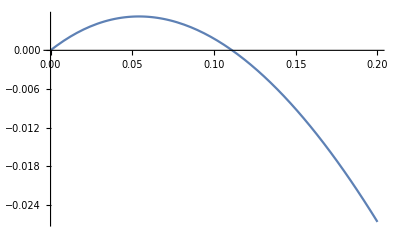

The optimal amount of X to tender is: Δ_X =   0.0540925

The amount out is: Δ_Y =   -0.102633

The resulting reserves are: (x_1,y_1) =   {1.05409,1.89737}

The marginal price paid was: P_M =   1.89737

The final price of the pool is: P =   1.8

-S+((L w x (y/x)^w+(v-v w+x) y (-1+γ)) ((v+x)^-w (L-v (y/x)^(1-w) (-1+γ)))^(1/(1-w)))/((-1+w) (v+x) (-L x (y/x)^w+v y (-1+γ)))

```mathematica
Subscript[S, ext] = 1.8; Assert[Subscript[S, ext] < Subscript[S, 0]];
Subscript[Prof, Lower][in_] := Subscript[V, A][Subscript[P, M][in,Subscript[Δ, Y][in,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]]], Subscript[S, ext], in]
Plot[Subscript[Prof, Lower][v], {v,0,0.2}]
Subscript[O, X] = ArgMax[{Subscript[Prof, Lower][x], 0<=x<=5}, x]; 
Echo[Subscript[O, X], "The optimal amount of X to tender is: Δ_X = "];
Echo[N[Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]],18], "The amount out is: Δ_Y = "];
Echo[{Subscript[x, 0] + Subscript[O, X], Subscript[y, 0] + Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]]}, "The resulting reserves are: (x_1,y_1) = "];
Echo[Subscript[P, M][Subscript[O, X],Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]]], "The marginal price paid was: P_M = "];
Subscript[P, F] = P[Subscript[x, 0] + Subscript[O, X], Subscript[y, 0]+Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[w, 0]]; Echo[N[Subscript[P, F],18], "The final price of the pool is: P = "];
FullSimplify[D[Subscript[V, A][Subscript[P, M][v,Subscript[Δ, Y][v,x,y,L,w,γ]], S, v],v]]
(* Check that the trading function is invariant under the swap *)
Assert[Abs[φ[Subscript[x, 0] + Subscript[O, X], Subscript[y, 0] + Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[L, 0] + Subscript[δ, LiqX][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[w, 0]]] < 10^-15]
```

### Raise External Price:

#### Let O_Y be the optimal amount of Y token to tender to get max arbitrage profit.

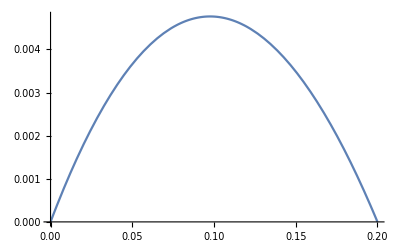

The optimal amount of Y to tender is: Δ_Y =   0.0976177

The amount out is: Δ_X =   -0.0465374

The resulting reserves are: (x_1,y_1) =   {0.953463,2.09762}

The marginal price paid was: P_M =   2.09762

The final price of the pool is: P =   2.2

-S+(2 v w x (v+y) (-L+v (x/y)^w (-1+γ))+v ((v+y)^(-1+w) (L-v (x/y)^w (-1+γ)))^(1/w) (L (v+v w+2 w y)-v (x/y)^w (v w-y+2 w y) (-1+γ)))/(w (v+y) (x-((v+y)^(-1+w) (L-v (x/y)^w (-1+γ)))^(1/w))^2 (-L+v (x/y)^w (-1+γ)))

```mathematica
Subscript[S, ext] = 2.2; Assert[Subscript[S, ext] > Subscript[S, 0]];
Subscript[Prof, Raise][in_] := Subscript[V, A][Subscript[P, M][Subscript[Δ, X][in,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]],in], Subscript[S, ext], Subscript[Δ, X][in,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]]]
Plot[Subscript[Prof, Raise][v], {v,0,0.2}]
Subscript[O, Y] = ArgMax[{Subscript[Prof, Raise][y], 0<=y<=5}, y]; 
Echo[Subscript[O, Y], "The optimal amount of Y to tender is: Δ_Y = "];
Echo[N[Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]],18], "The amount out is: Δ_X = "];
Echo[{Subscript[x, 0] + Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[y, 0] + Subscript[O, Y]}, "The resulting reserves are: (x_1,y_1) = "];
Echo[Subscript[P, M][Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]],Subscript[O, Y]], "The marginal price paid was: P_M = "];
Subscript[P, F] = P[Subscript[x, 0] + Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[y, 0]+Subscript[O, Y], Subscript[w, 0]]; Echo[N[Subscript[P, F],18], "The final price of the pool is: P = "];
FullSimplify[D[Subscript[V, A][Subscript[P, M][Subscript[Δ, X][v,x,y,L,w,γ],v], S, v],v]]
(* Check that the trading function is invariant under the swap *)
Assert[Abs[φ[Subscript[x, 0] + Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[y, 0] + Subscript[O, Y], Subscript[L, 0] + Subscript[δ, LiqX][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[w, 0],Subscript[γ, 0]], Subscript[w, 0]]] < 10^-15]
```